## Rigid, θx<θy, qx1<qx2, qy1<qy2

```mathematica
g[x_,y_,θx_,θy_,qx1_,qx2_,qy1_,qy2_]:= (x-qx1) (θx-If[x<=qx1,1,0])-(x-qx2) (θx-If[x<=qx2,1,0])+
 (y-qy1) (θy-If[y<=qy1,1,0])-(y-qy2) (θy-If[y<=qy2,1,0]);
h[x_,y_,θx_,θy_,qx1_,qx2_,qy1_,qy2_]:= Sign[g[x,y,θx,θy,qx1,qx2,qy1,qy2]];
```

```mathematica
gInteract[x_,y_,θx_,θy_,qx1_,qx2_,qy1_,qy2_]:= (x-qx1) (θx-If[x<=qx1,1,0])-(x-qx2) (θx-If[x<=qx2,1,0])+
 (y-qy1) (θy-If[y<=qy1,1,0])-(y-qy2) (θy-If[y<=qy2,1,0])-
((x-qx1) (θx-If[x<=qx1,1,0])-(x-qx2) (θx-If[x<=qx2,1,0]))*((y-qy1) (θy-If[y<=qy1,1,0])-(y-qy2) (θy-If[y<=qy2,1,0]));
hInteract[x_,y_,θx_,θy_,qx1_,qx2_,qy1_,qy2_]:= Sign[gInteract[x,y,θx,θy,qx1,qx2,qy1,qy2]];
```

```mathematica
gInteract2[x_,y_,θx_,θy_,qx1_,qx2_,qy1_,qy2_]:= 
((x-qx1) (θx-If[x<=qx1,1,0])-(x-qx2) (θx-If[x<=qx2,1,0]))*((y-qy1) (θy-If[y<=qy1,1,0])-(y-qy2) (θy-If[y<=qy2,1,0]));
hInteract2[x_,y_,θx_,θy_,qx1_,qx2_,qy1_,qy2_]:= Sign[gInteract2[x,y,θx,θy,qx1,qx2,qy1,qy2]];
```

### case 1: qx1<qx2, qy1<qy2

```mathematica
Collect[Simplify[g[x,y,θx,θy,qx1,qx2,qy1,qy2],Assumptions->θx<θy && qx1<qx2&&qy1<qy2 && x<=qx1&&y≤qy1],x]
```

qx1+qx2 (-1+θx)-qx1 θx-(qy1-qy2) (-1+θy)

```mathematica
Plot3D[g[x,y,0.5,0.5,1,2,0,3],{x,-4,4},{y,-5,5}]
```

-Graphics3D-

```mathematica
Plot3D[h[x,y,0.5,0.5,1,2,0,3],{x,-4,4},{y,-5,5}]
```

-Graphics3D-

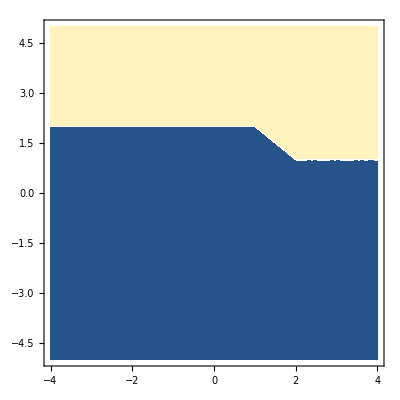

```mathematica
ContourPlot[h[x,y,0.5,0.5,1,2,0,3],{x,-4,4},{y,-5,5}]
```

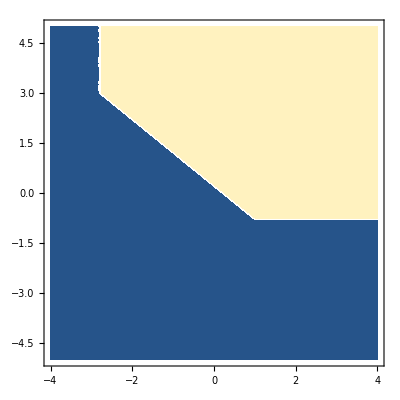

```mathematica
ContourPlot[h[x,y,0.2,0.5,-3,1,-3,3],{x,-4,4},{y,-5,5}]
```

```mathematica
5
```

-Graphics3D-

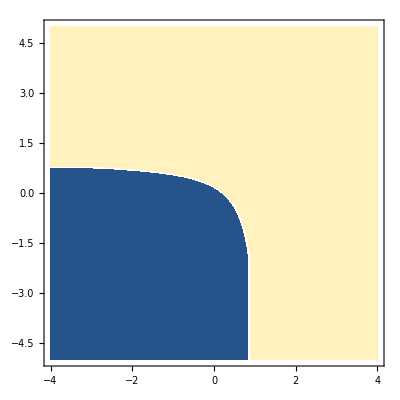

```mathematica
Plot3D[hInteract[x,y,0.2,0.5,-3,1,-2,2],{x,-4,4},{y,-5,5}]
ContourPlot[hInteract[x,y,0.2,0.5,-3,1,-2,2],{x,-4,4},{y,-5,5}]
```

-Graphics3D-

-Graphics3D-

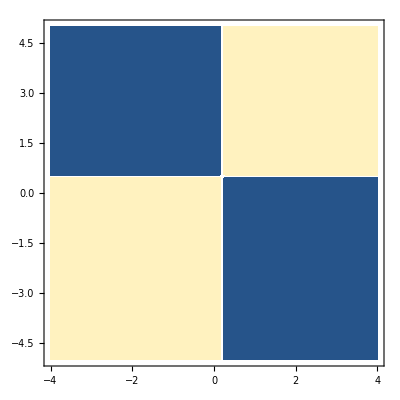

```mathematica
Plot3D[gInteract2[x,y,0.2,0.5,-3,1,-2,3],{x,-4,4},{y,-5,5}]
Plot3D[hInteract2[x,y,0.2,0.5,-3,1,-2,3],{x,-4,4},{y,-5,5}]
ContourPlot[hInteract2[x,y,0.2,0.5,-3,1,-2,3],{x,-4,4},{y,-5,5}]
```

## Rigid, θx1<θy1,θx2<θy2, qx1<qx2, qy1<qy2

```mathematica
g[x_,y_,θx_,θy_,qx1_,qx2_,qy1_,qy2_]:= (x-qx1) (θx-If[x<=qx1,1,0])-(x-qx2) (θx-If[x<=qx2,1,0])+
 (y-qy1) (θy-If[y<=qy1,1,0])-(y-qy2) (θy-If[y<=qy2,1,0]);
h[x_,y_,θx_,θy_,qx1_,qx2_,qy1_,qy2_]:= Sign[g[x,y,θx,θy,qx1,qx2,qy1,qy2]];
```